### Start choosing the example:

```mathematica
t=22;
beta =0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

EEX: j395==jt399&&j394==jt400&&j391==jt401&&j396==jt402&&j392==jt403&&j397==jt404&&j391==jt400&&j398==jt399&&j395==jt402&&j392==jt401&&j396==jt404&&j393==jt403&&j394==80&&u411==15&&-u408+u412==0&&-u407+u411==0&&jt399==0&&jt404==0&&j391-j395-u405+u409==0&&j392-j396-u406+u410==0

EEX: -u405+u408==0.&&-80+u405-u406==0.&&-95+u406==0.

D2E: {True,<|j394→80,u411→15,j391→80,j392→80,j393→80,j395→0,j396→0,j397→0,j398→0,jt399→0,jt400→80,jt401→80,jt402→0,jt403→80,jt404→0,u407→15,u409→-80+175.,u410→-80+95.,u412→175.,u405→175.,u406→95.,u408→175.|>}

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.013339,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j391→80,j392→80,j393→80,j394→80,j395→0,j396→0,j397→0,j398→0,jt399→0,jt400→80,jt401→80,jt402→0,jt403→80,jt404→0,u405→175.,u406→95.,u407→15,u408→175.,u409→-80+175.,u410→-80+95.,u411→15,u412→175.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==78.6594&&95.-u280==78.6594

FRX1: The Error on the nonlinear terms is 5.65233×10^-15

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==78.6594&&95.-u280==78.6594

FRX1: The Error on the nonlinear terms is 5.65233×10^-15

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→17.6812,u280→16.3406,u281→15,u282→0.+1. 17.6812,u283→0.+1. 16.3406,u284→15.,u285→15,u286→0.+1. 17.6812|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==78.3376&&95.-u280==78.3376

FRX1: The Error on the nonlinear terms is 7.53644×10^-15

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==78.3376&&95.-u280==78.3376

FRX1: The Error on the nonlinear terms is 7.53644×10^-15

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→18.3249,u280→16.6624,u281→15,u282→0.+1. 18.3249,u283→0.+1. 16.6624,u284→15.,u285→15,u286→0.+1. 18.3249|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==77.2418&&95.-u280==77.2418

FRX1: The Error on the nonlinear terms is 8.79252×10^-15

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==77.2418&&95.-u280==77.2418

FRX1: The Error on the nonlinear terms is 8.79252×10^-15

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→20.5164,u280→17.7582,u281→15,u282→0.+1. 20.5164,u283→0.+1. 17.7582,u284→15.,u285→15,u286→0.+1. 20.5164|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==41.9663&&95.-u280==41.9663

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==41.9663&&95.-u280==41.9663

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→91.0675,u280→53.0337,u281→15,u282→0.+1. 91.0675,u283→0.+1. 53.0337,u284→15.,u285→15,u286→0.+1. 91.0675|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==0&&95.-u280==0

FRX1: The Error on the nonlinear terms is 1.20583×10^-13

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→175.,u280→95.,u281→15,u282→0.+1. 175.,u283→0.+1. 95.,u284→15.,u285→15,u286→0.+1. 175.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-538.355&&95.-u280==-538.355

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-538.355&&95.-u280==-538.355

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→1251.71,u280→633.355,u281→15,u282→0.+1. 1251.71,u283→0.+1. 633.355,u284→15.,u285→15,u286→0.+1. 1251.71|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-286137.&&95.-u280==-286137.

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-286137.&&95.-u280==-286137.

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→572448.,u280→286232.,u281→15,u282→0.+1. 572448.,u283→0.+1. 286232.,u284→15.,u285→15,u286→0.+1. 572448.|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.71596×10^7&&95.-u280==-1.71596×10^7

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.71596×10^7&&95.-u280==-1.71596×10^7

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→3.43194×10^7,u280→1.71597×10^7,u281→15,u282→0.+1. 3.43194×10^7,u283→0.+1. 1.71597×10^7,u284→15.,u285→15,u286→0.+1. 3.43194×10^7|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.72477×10^7&&95.-u280==-1.72477×10^7

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.72477×10^7&&95.-u280==-1.72477×10^7

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→3.44956×10^7,u280→1.72478×10^7,u281→15,u282→0.+1. 3.44956×10^7,u283→0.+1. 1.72478×10^7,u284→15.,u285→15,u286→0.+1. 3.44956×10^7|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-2.22357×10^7&&95.-u280==-2.22357×10^7

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-2.22357×10^7&&95.-u280==-2.22357×10^7

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→4.44716×10^7,u280→2.22358×10^7,u281→15,u282→0.+1. 4.44716×10^7,u283→0.+1. 2.22358×10^7,u284→15.,u285→15,u286→0.+1. 4.44716×10^7|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-2.90056×10^7&&95.-u280==-2.90056×10^7

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-2.90056×10^7&&95.-u280==-2.90056×10^7

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→5.80115×10^7,u280→2.90057×10^7,u281→15,u282→0.+1. 5.80115×10^7,u283→0.+1. 2.90057×10^7,u284→15.,u285→15,u286→0.+1. 5.80115×10^7|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-5.04043×10^7&&95.-u280==-5.04043×10^7

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-5.04043×10^7&&95.-u280==-5.04043×10^7

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→1.00809×10^8,u280→5.04044×10^7,u281→15,u282→0.+1. 1.00809×10^8,u283→0.+1. 5.04044×10^7,u284→15.,u285→15,u286→0.+1. 1.00809×10^8|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-3.19735×10^8&&95.-u280==-3.19735×10^8

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-3.19735×10^8&&95.-u280==-3.19735×10^8

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→6.39469×10^8,u280→3.19735×10^8,u281→15,u282→0.+1. 6.39469×10^8,u283→0.+1. 3.19735×10^8,u284→15.,u285→15,u286→0.+1. 6.39469×10^8|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.58135×10^10&&95.-u280==-1.58135×10^10

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.58135×10^10&&95.-u280==-1.58135×10^10

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→3.1627×10^10,u280→1.58135×10^10,u281→15,u282→0.+1. 3.1627×10^10,u283→0.+1. 1.58135×10^10,u284→15.,u285→15,u286→0.+1. 3.1627×10^10|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.3601×10^16&&95.-u280==-1.3601×10^16

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-1.3601×10^16&&95.-u280==-1.3601×10^16

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→2.7202×10^16,u280→1.3601×10^16,u281→15,u282→0.+1. 2.7202×10^16,u283→0.+1. 1.3601×10^16,u284→15.,u285→15,u286→0.+1. 2.7202×10^16|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-9.50252×10^33&&95.-u280==-9.50252×10^33

FRX1: The Error on the nonlinear terms is 0.

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==-9.50252×10^33&&95.-u280==-9.50252×10^33

FRX1: The Error on the nonlinear terms is 0.

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→1.9005×10^34,u280→9.50252×10^33,u281→15,u282→0.+1. 1.9005×10^34,u283→0.+1. 9.50252×10^33,u284→15.,u285→15,u286→0.+1. 1.9005×10^34|>

```mathematica
alpha = 1.99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j395==jt399&&j394==jt400&&j391==jt401&&j396==jt402&&j392==jt403&&j397==jt404&&j391==jt400&&j398==jt399&&j395==jt402&&j392==jt401&&j396==jt404&&j393==jt403&&j394==80&&u411==15&&-u408+u412==0&&-u407+u411==0&&jt399==0&&jt404==0

EEX: -u405+u408==0.&&-u406+u409==0.&&-15+u410==0.

EEX: 80.-u405+1. u406==-1.99061×10^105&&95.-u406==-1.99061×10^105

FRX1: The Error on the nonlinear terms is 0.

EEX: j395==jt399&&j394==jt400&&j391==jt401&&j396==jt402&&j392==jt403&&j397==jt404&&j391==jt400&&j398==jt399&&j395==jt402&&j392==jt401&&j396==jt404&&j393==jt403&&j394==80&&u411==15&&-u408+u412==0&&-u407+u411==0&&jt399==0&&jt404==0

EEX: -u405+u408==0.&&-u406+u409==0.&&-15+u410==0.

EEX: 80.-u405+1. u406==-1.99061×10^105&&95.-u406==-1.99061×10^105

FRX1: The Error on the nonlinear terms is 0.

<|j391→80,j392→80,j393→80,j394→80,j395→0,j396→0,j397→0,j398→0,jt399→0,jt400→80,jt401→80,jt402→0,jt403→80,jt404→0,u405→3.98121×10^105,u406→1.99061×10^105,u407→15,u408→0.+1. 3.98121×10^105,u409→0.+1. 1.99061×10^105,u410→15.,u411→15,u412→0.+1. 3.98121×10^105|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j269==jt273&&j268==jt274&&j265==jt275&&j270==jt276&&j266==jt277&&j271==jt278&&j265==jt274&&j272==jt273&&j269==jt276&&j266==jt275&&j270==jt278&&j267==jt277&&j268==80&&u285==15&&-u282+u286==0&&-u281+u285==0&&jt273==0&&jt278==0

EEX: -u279+u282==0.&&-u280+u283==0.&&-15+u284==0.

EEX: 80.-u279+1. u280==0&&95.-u280==0

FRX1: The Error on the nonlinear terms is 1.20583×10^-13

<|j265→80,j266→80,j267→80,j268→80,j269→0,j270→0,j271→0,j272→0,jt273→0,jt274→80,jt275→80,jt276→0,jt277→80,jt278→0,u279→175.,u280→95.,u281→15,u282→0.+1. 175.,u283→0.+1. 95.,u284→15.,u285→15,u286→0.+1. 175.|>

### What we this plot for?

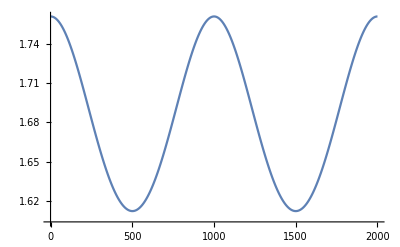

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.